Comparing Heat Transfer in a Rectangular and a Pin Fin

```mathematica
Manipulate[
Module[{t,w,L,u,Cp,ka,ν,ρ,μ,Pr,Rex,h,P,Ac,k,Tb,m,qf,T,ϵf,xT,col},
t=0.0015;(*m thickness*)
w=0.02;(*width*)
L=length/1000;(*length*)

(*air properties*)
u=1;(*m/s*)
Cp=1005;(*J/kg/K*)
ka=0.0264;(*W/m/K*)
ν=1.71*^-5;(*m2/s*)
ρ=1.164;(*kg/m3*)
μ=ν*ρ;(*N s/m2*)

Pr=(Cp*μ)/ka;
Rex=(u*If[fin==1,w,t])/ν;
h=ha/.First@If[fin==1,Solve[(ha*w)/ka==0.664*Rex^(1/2)*Pr^(1/3),ha],Solve[(ha*t)/ka==0.683*Rex^0.466*Pr^(1/3),ha]];

If[fin==1,{P=2*w+2*t;Ac=w*t},{P=π*t;Ac=π*t^2/4;}];

(*therm. data*)
k=Which[
mat==1,14,(*s.steel*)
mat==2,60.5,(*carbon steel*)
mat==3,80.2,(*iron*)
mat==4,110,(*brass*)
mat==5,237,(*aluminum*)
mat==6,401(*copper*)
];(*W/m/K*)

Tb=500;
m=√((h*P)/(k*Ac));
qf=(Tb-Ta)*√(h*P*k*Ac)*Tanh[m*L];
T[x_]=(Tb-Ta)*Cosh[m*(L-x)]/Cosh[m*L]+Ta;
ϵf=qf/(h*w*t*(Tb-Ta));

(*xT=Evaluate@Interpolation[Transpose[{Range[500,273,-1],Evaluate@Table[x/.Quiet@FindRoot[250+23.72*Cosh[152.3*(1/50-x)]==t,{x,0}],{t,273,500,1}]}]];*)

(*xT=Evaluate@Interpolation[Transpose[{Range[500,273,-1],Evaluate@Table[x/.Quiet@FindRoot[250+37.24*Cosh[129.6*(1/50-x)]==temp,{x,0}],{temp,273,500,1}]}]];*)
(*xT[x_]:=7*^-14*x^5-1*^-10*x^4+7*^-8*x^3-2*^-5*x^2+0.0035*x-0.2135;*)

xT[x_]:=2.195*^-11*x^4-3.059*^-8*x^3+1.5999*^-5*x^2-0.003676*x+0.3118;
col[x_]:=ColorData["TemperatureMap"][Rescale[xT[T[x]],{0,0.02}]];

Grid[{
{Text@Style[Column[{
Row[{"fin heat transfer rate = ",NumberForm[qf,{3,2}]," W"}],
Row[{"temperature of fin tip = ",NumberForm[T[L],{3,0}]," K"}],
Row[{"fin effectiveness = ",NumberForm[ϵf,{3,2}]}]
},Alignment->"="],17],SpanFromLeft},
{Show[
Graphics3D[{{col[0],Cuboid[{-0.0025,-w/2,-w/2},{0,w/2,w/2}]},Text[Style["base = 500 K",18],{0,0,0.0075},{0,0},{2,0.35}]}],
Switch[fin,
1,RegionPlot3D[z<t,{x,0,L},{y,-w/2,w/2},{z,0,t},Mesh->None,ColorFunction->(col[#1]&),ColorFunctionScaling->False],
2,Show[Graphics3D[{col[L],Cylinder[{{0.999*L,0,0},{L,0,0}},t/2]}],
ParametricPlot3D[{x,t/2*Sin[θ],t/2*Cos[θ]},{θ,0,2*π},{x,0,L},Mesh->None,ColorFunction->(col[#1]&),ColorFunctionScaling->False]]
],Boxed->False,ViewPoint->{2,-2,1},Lighting->"Neutral",ImageSize->{300,315}],
DensityPlot[xT[x],{y,0,1},{x,273,500},ColorFunction->"TemperatureMap",PlotPoints->50,
Epilog->{Line[{{-0.5,T[L]},{1,T[L]}}],Text[Style[NumberForm[T[L],{3,0}],17],{-0.5,T[L]},{1,0}]},
PlotRange->{{-1,1},{273,500}},PlotRangePadding->{{0.1,None},5},Frame->{{None,True},{None,None}},FrameTicks->All,FrameStyle->Black,LabelStyle->17,AspectRatio->Full,ImageSize->{150,315}],
Rotate[Text@Style["temperature  (K)",17],π/2]}
}]

(*Plot[{xT[x],3*10^-9*x^3-3*10^-6*x^2+0.0009*x-0.1064},{x,273,500},PlotStyle->{{Thick,Blue},{Thick,Dashed,Black}}]*)

(*Fit[Transpose[{Range[500,273,-1],Evaluate@Table[x/.Quiet@FindRoot[250+37.24*Cosh[129.6*(1/50-x)]==temp,{x,0}],{temp,273,500,1}]}],{1,y,y^2,y^3},y];

Plot[{xT[y],0.31179069950013744-0.0036761202953850543 y+0.000015999344413521673 y^2-3.058886414914488*^-8 y^3+2.1951828071422827*^-11 y^4,-0.14185779861726217+0.0012045371597881906 y-3.431425963038368*^-6 y^2+3.348662049274599*^-9 y^3},{y,273,500},PlotStyle->{{Thick,Blue},{Thick,Dashed,Black},{Thick,Dotted,Orange}},Axes->None,Frame->True]*)
],
Column[{
Row[{
Control[{{fin,1,"fin type:"},{1->" rectangular ",2->" pin "},Setter}],Spacer[20],
Control[{{mat,1,"material:"},{1->"stainless steel",2->"carbon steel",3->"iron",4->"brass",5->"aluminum",6->"copper"},PopupMenu}]
}],
Control[{{length,10,"fin length (mm)"},5,20,1,Appearance->"Labeled"}],
Control[{{Ta,300,"ambient temperature (K)"},250,350,1,Appearance->"Labeled"}]
}]
]
```

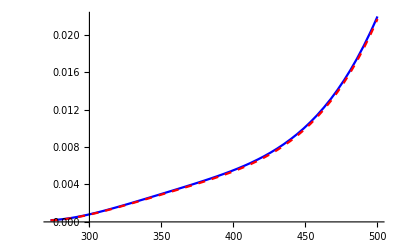

```mathematica
Plot[{0.31179069950013744-0.0036761202953850543 x+0.000015999344413521673 x^2-3.058886414914488*^-8 x^3+2.1951828071422827*^-11 x^4,2.195*^-11*x^4-3.059*^-8*x^3+1.5999*^-5*x^2-0.003676*x+0.3118},{x,273,500},PlotStyle->{Blue,{Dashed,Red}}]
```

Heat transfer through a single fin (either a rectangular or pin fin) is calculated. The fin is mounted on a heat sink, the fin length and the ambient air temperature are varied using sliders. Select the fin material from the drop-down menu. The temperature distribution is shown on the fin surface using a color scale (red=hottest, blue=coolest), the temperature of the fin tip is shown on the right with the legend. The fin tip is assumed to be adiabatic and the air flow is laminar. The thickness of the rectangular fin, and diameter of the pin fin is 1.5 mm.





The heat transfer coefficient of air (h) is calculated using Nusselt correlations for laminar flow over a flat plate and a cylinder. Air properties are evaluated at 300 K. The average Nusselt (Nu_x) and Reynold's (Re_x) numbers are:

Nu_x=(h x)/k_a

Re_x=(u x)/ν

where x=w for a rectangular fin, and x=t for a pin fin, w is width and t is thickness/diameter (m), k_a is the thermal conductivity of air (W/m/k), u is the velocity of air (m/s), ν is the kinematic viscosity of air (m^2/s), h is in units of W/m^2/K, and Nu_x and Re_x are unitless.

For a rectangular fin:

Nu_x=0.664 Re_x^(1/2) Pr^(1/3)

For a pin fin:

Nu_x=0.683 Re_x^0.466 Pr^(1/3)

and Pr is the Prandtl number:

Pr=(Cp μ)/k_a

where Cp is the heat capacity of air (J/kg/K), μ is the dynamic viscosity of air (N s/m^2), and Pr is unitless.

For a fin with a tip that is assumed to be adiabatic:

T=T_∞+(Cosh(m (L-z)))/(Cosh(m L)) (T_b-T_∞)

q_f=√(h P k Ac) Tanh(m L) (T_b-T_∞)

where T is temperature (K), T_∞ is the ambient air temperature, T_b=500 K is the base temperature, m is a simplification term, L is the fin length (m), z is distance down the fin, q_f is the fin heat transfer rate (W), P is the fin perimeter (m), Ac is the fin cross-section area (m^2), and k is the thermal conductivity of the material (W/m/K).

m=√((h P)/(k Ac))

For a rectangular fin:

P=2 w+2 t

Ac=w t

For a pin fin:

P=π t

Ac=π/4 t^2

The thermal conductivities (W/m/K) of the fin materials are:

stainless steel	k=14

carbon steel		k=60.5

iron			k=80.2

brass			k=110

aluminum		k=237

copper			k=401

Resize Images

Rotate and Zoom in 3D

Drag Locators

Create and Delete Locators

Slider Zoom

Gamepad Controls

Automatic Animation

Bookmark Animation

fin heat transfer

Nusselt number

chemical engineering

mechanical engineering

conduction

convection

Contributed by: Rachael L. Baumann

Additional contributions by: John L. Falconer

(University of Colorado Boulder, Department of Chemical and Biological Engineering)